```mathematica
(* KINEMATICS PAPER*)

(* Mean (with S.D.) FOOTFALL PATTERNS
pooled data from 23 trials (8 animals) *)
```

```mathematica
(*********************************************************)
```

```mathematica
(* Determine operating system *)

os=$OperatingSystem;
frogworkpath="C:\\YOUR FILE DIRECTORY HERE\\" (*Set your main file directory, not to the folder where raw or archived data are stored*)
(*e.g. frogworkpath="C:\\Users\\Documents\\"*)
(*for Mac users change "C:\\" to "\\Volumes\\"*)

dataDirectory="YOUR DIRECTORY FOOTFALL PATTERN DATA"; (*Set the directory where the footfall pattern data is located*)

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

(**************************************************************)

importedrawfootfalldata=Import["Footfall Pattern Data.xlsx","Data"];
rawfootfalldata=Transpose[importedrawfootfalldata[[1,1;;27,1;;16]]];

Dimensions[rawfootfalldata]
rawfootfalldata[[;;,27]]
(*16 columns, 27 rows*)


(* FOOTFALL DATA ROWS;
                  
KM01_RUN_02 = 1;

KM02_RUN_01 = 2;
KM02_RUN_02 = 3;
KM02_RUN_09 = 4;

KM04_RUN_09 = 5;
KM04_RUN_11 = 6;
KM04_RUN_12 = 7;

KM05_RUN_04 = 8;
KM05_RUN_08 = 9;

KM06_RUN_11 = 10;
KM06_RUN_12 = 11;
KM06_RUN_13 = 12;
KM06_RUN_15 = 13;
KM06_RUN_16 = 14;

KM07_RUN_14 = 15;
KM07_RUN_16 = 16;
KM07_RUN_17 = 17;

KM08_RUN_09 = 18;
KM08_RUN_10 = 19;

KM23_RUN_01 = 20;
KM23_RUN_02 = 21;
KM23_RUN_03 = 22;
KM23_RUN_05 = 23;

Averages = 24;
SD = 25;
Average - SD = 26;
Average + SD = 27;

*)


(*FOOTFALL DATA COLUMNS;

Right Hindlimb: Block 1 = 1-2, Block 2 = 3-4, 
Left Forelimb: Block 1 = 5-6, Block 2 = 7-8, 
Left Hindlimb: Block 1 = 9-10, Block 2 = 11-12, 
Right Forelimb: Block 1 = 13-14, Block 2 = 15-16, 

*)
```

{16,27}

{0.,75.3331,100.,200.,-4.58981,69.5264,92.5702,200.,-7.37625,31.6923,52.4744,200.,-7.44812,17.281,43.4605,200.}

```mathematica
(*********************************************************)
```

```mathematica
(*USER INPUT*)

percentavfootfalldatarow=24;
percentavminussdfootfalldatarow=26;
percentavplussdfootfalldatarow=27;
data="RUN";
```

```mathematica
(*********************************************************)
```

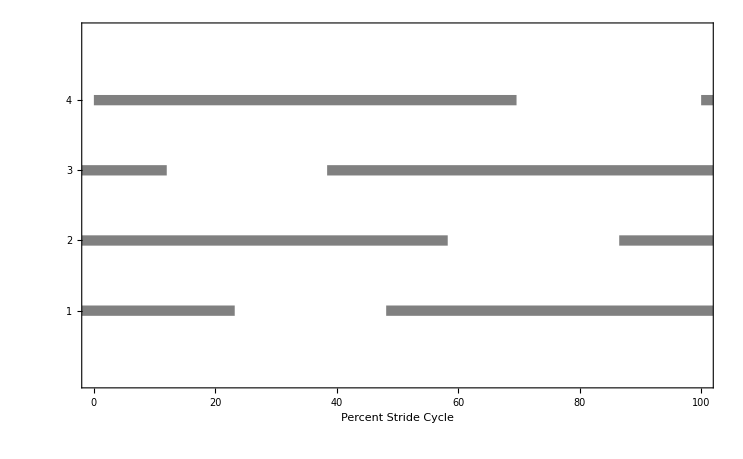

```mathematica
(*Mean footfall*)
percentavfootfallstyle={PlotStyle->{Gray,Thickness[0.01]},Frame->{{True,False},{True,False}},FrameTicks->{{0,10,20,30,40,50,60,70,80,90,100},{1,2,3,4}},FrameLabel->{"Percent Stride Cycle",None},LabelStyle->{Black,Larger},PlotRange->{{0,100},{0,5}}};

pavrh1=ListLinePlot[{{rawfootfalldata[[1,percentavfootfalldatarow]],4},{rawfootfalldata[[2,percentavfootfalldatarow]],4}},percentavfootfallstyle];
pavlf1=ListLinePlot[{{rawfootfalldata[[5,percentavfootfalldatarow]],2},{rawfootfalldata[[6,percentavfootfalldatarow]],2}},percentavfootfallstyle];
pavlh1=ListLinePlot[{{rawfootfalldata[[9,percentavfootfalldatarow]],1},{rawfootfalldata[[10,percentavfootfalldatarow]],1}},percentavfootfallstyle];
pavrf1=ListLinePlot[{{rawfootfalldata[[13,percentavfootfalldatarow]],3},{rawfootfalldata[[14,percentavfootfalldatarow]],3}},percentavfootfallstyle];

pavg1=Show[pavrf1,pavlh1,pavlf1,pavrh1];

pavrh2=ListLinePlot[{{rawfootfalldata[[3,percentavfootfalldatarow]],4},{rawfootfalldata[[4,percentavfootfalldatarow]],4}},percentavfootfallstyle];
pavlf2=ListLinePlot[{{rawfootfalldata[[7,percentavfootfalldatarow]],2},{rawfootfalldata[[8,percentavfootfalldatarow]],2}},percentavfootfallstyle];
pavlh2=ListLinePlot[{{rawfootfalldata[[11,percentavfootfalldatarow]],1},{rawfootfalldata[[12,percentavfootfalldatarow]],1}},percentavfootfallstyle];
pavrf2=ListLinePlot[{{rawfootfalldata[[15,percentavfootfalldatarow]],3},{rawfootfalldata[[16,percentavfootfalldatarow]],3}},percentavfootfallstyle];

pavg2=Show[pavrf2,pavlh2,pavlf2,pavrh2];


PercentAveragefootfall=Show[pavg1,pavg2]
```

```mathematica
(***********************************************************)
```

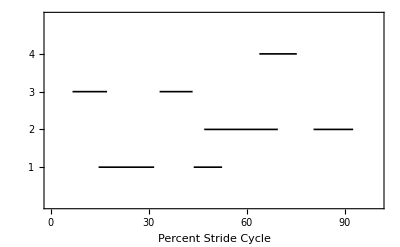

```mathematica
(*Mean footfall+/- SD*)

percentavsdfootfallstyle={PlotStyle->{Black,Thickness[0.003]},Frame->{{True,False},{True,False}},FrameTicks->{{0,10,20,30,40,50,60,70,80,90,100},{1,2,3,4}},FrameLabel->{"Percent Stride Cycle",None},LabelStyle->{Black,Larger},PlotRange->{{0,100},{0,5}}};

pavsdrh1a=ListLinePlot[{{rawfootfalldata[[1,percentavminussdfootfalldatarow]],4},{rawfootfalldata[[1,percentavplussdfootfalldatarow]],4}},percentavsdfootfallstyle];
pavsdrh1b=ListLinePlot[{{rawfootfalldata[[2,percentavminussdfootfalldatarow]],4},{rawfootfalldata[[2,percentavplussdfootfalldatarow]],4}},percentavsdfootfallstyle];
pavsdrh1=Show[pavsdrh1a,pavsdrh1b];


pavsdlf1a=ListLinePlot[{{rawfootfalldata[[5,percentavminussdfootfalldatarow]],2},{rawfootfalldata[[5,percentavplussdfootfalldatarow]],2}},percentavsdfootfallstyle];
pavsdlf1b=ListLinePlot[{{rawfootfalldata[[6,percentavminussdfootfalldatarow]],2},{rawfootfalldata[[6,percentavplussdfootfalldatarow]],2}},percentavsdfootfallstyle];

pavsdlf1=Show[pavsdlf1a,pavsdlf1b];


pavsdlh1a=ListLinePlot[{{rawfootfalldata[[9,percentavminussdfootfalldatarow]],1},{rawfootfalldata[[9,percentavplussdfootfalldatarow]],1}},percentavsdfootfallstyle];
pavsdlh1b=ListLinePlot[{{rawfootfalldata[[10,percentavminussdfootfalldatarow]],1},{rawfootfalldata[[10,percentavplussdfootfalldatarow]],1}},percentavsdfootfallstyle];

pavsdlh1=Show[pavsdlh1a,pavsdlh1b];


pavsdrf1a=ListLinePlot[{{rawfootfalldata[[13,percentavminussdfootfalldatarow]],3},{rawfootfalldata[[13,percentavplussdfootfalldatarow]],3}},percentavsdfootfallstyle];
pavsdrf1b=ListLinePlot[{{rawfootfalldata[[14,percentavminussdfootfalldatarow]],3},{rawfootfalldata[[14,percentavplussdfootfalldatarow]],3}},percentavsdfootfallstyle];

pavsdrf1=Show[pavsdrf1a,pavsdrf1b];

pavsdg1=Show[pavsdrf1,pavsdlh1,pavsdlf1,pavsdrh1];



pavsdrh2a=ListLinePlot[{{rawfootfalldata[[3,percentavminussdfootfalldatarow]],4},{rawfootfalldata[[3,percentavplussdfootfalldatarow]],4}},percentavsdfootfallstyle];
pavsdrh2b=ListLinePlot[{{rawfootfalldata[[4,percentavminussdfootfalldatarow]],4},{rawfootfalldata[[4,percentavplussdfootfalldatarow]],4}},percentavsdfootfallstyle];

pavsdrh2=Show[pavsdrh2a,pavsdrh2b];


pavsdlf2a=ListLinePlot[{{rawfootfalldata[[7,percentavminussdfootfalldatarow]],2},{rawfootfalldata[[7,percentavplussdfootfalldatarow]],2}},percentavsdfootfallstyle];
pavsdlf2b=ListLinePlot[{{rawfootfalldata[[8,percentavminussdfootfalldatarow]],2},{rawfootfalldata[[8,percentavplussdfootfalldatarow]],2}},percentavsdfootfallstyle];

pavsdlf2=Show[pavsdlf2a,pavsdlf2b];


pavsdlh2a=ListLinePlot[{{rawfootfalldata[[11,percentavminussdfootfalldatarow]],1},{rawfootfalldata[[11,percentavplussdfootfalldatarow]],1}},percentavsdfootfallstyle];
pavsdlh2b=ListLinePlot[{{rawfootfalldata[[12,percentavminussdfootfalldatarow]],1},{rawfootfalldata[[12,percentavplussdfootfalldatarow]],1}},percentavsdfootfallstyle];

pavsdlh2=Show[pavsdlh2a,pavsdlh2b];

pavsdrf2a=ListLinePlot[{{rawfootfalldata[[15,percentavminussdfootfalldatarow]],3},{rawfootfalldata[[15,percentavplussdfootfalldatarow]],3}},percentavsdfootfallstyle];
pavsdrf2b=ListLinePlot[{{rawfootfalldata[[16,percentavminussdfootfalldatarow]],3},{rawfootfalldata[[16,percentavplussdfootfalldatarow]],3}},percentavsdfootfallstyle];

pavsdrf2=Show[pavsdrf2a,pavsdrf2b];

pavsdg2=Show[pavsdrf2,pavsdlh2,pavsdlf2,pavsdrh2];

PercentplusminusSDfootfall=Show[pavsdg1,pavsdg2]
```

```mathematica
(**************************************************************)
```

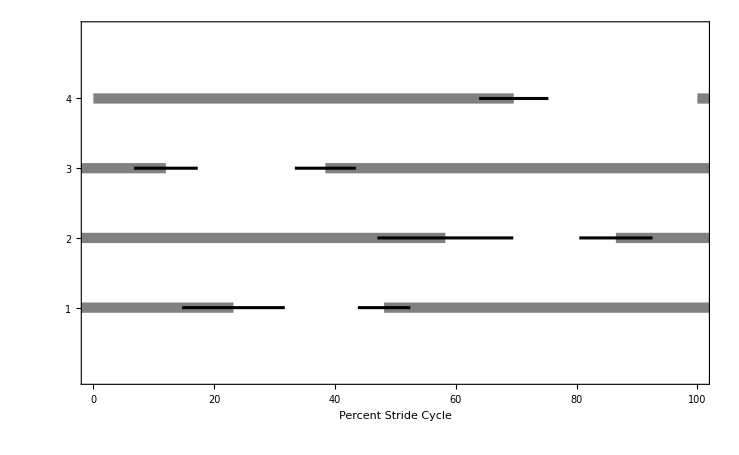

```mathematica
(*AVERAGE +/- SD plot*)

PercentAverageplusminusSDfootfall=Show[PercentAveragefootfall,PercentplusminusSDfootfall]
```

```mathematica
(**************************************************************)
```

```mathematica
(*Export*)
```

```mathematica
dataDirectory="YOUR DIRECTORY FOR EXPORTED FIGURES";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];


(*Average*)
Export["Kinematics Paper - Footfall patterns - Version 3.svg",PercentAveragefootfall]
(*Average +/- SD*)
Export["Kinematics Paper - Footfall patterns plus.minus SD - Version 3.svg",PercentAverageplusminusSDfootfall]
```

Kinematics Paper - Footfall patterns - Version 3.svg

Kinematics Paper - Footfall patterns plus.minus SD - Version 3.svg